# Homework 2: Exploring Least Squares Approximation Name: Rutvik Joshi

# Methods:

```mathematica
findCParameters[data_]:=Module[{l = 0,cParameters = Range[Length[data]]},
For[i=1,i<Length[data],i++,l = l +  Sqrt[(data[[i+1,1]] - data[[i,1]])^2+(data[[i+1,2]] - data[[i,2]])^2]];
cParameters[[1]] = 0;
For[i=2,i<=Length[data],i++,
cParameters[[i]]= cParameters[[i-1]] + (Sqrt[(data[[i,1]] - data[[i-1,1]])^2+(data[[i,2]] - data[[i-1,2]])^2])/l;];
cParameters]

findUParameters[data_] := Module[{uParameters = Range[Length[data]]},
For[i=1,i<=Length[data],i++,
uParameters[[i]] = data[[i,1]]/(data[[Length[data],1]]-data[[1,1]]);
];
uParameters]

findLinearSol[data_,knot_,degree_] := (
knotNo= Length[data] - 1;
(* forming vandermonde matrix*) 
vandermonde=Table[BernsteinBasis[degree,j-1,knot[[i]]],{i,1,knotNo+1},{j,1,degree+1}];
(* solving linear equations and returning the same*)
Return[LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data]];
)
```

# Part: 1

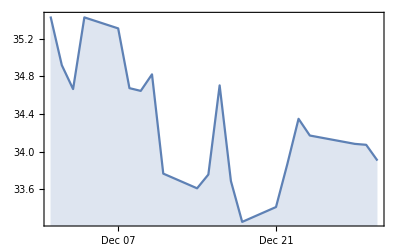

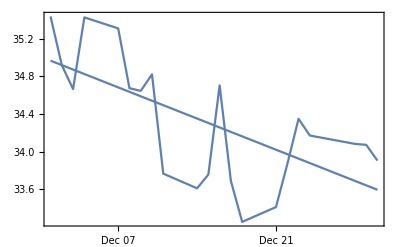

```mathematica
data = FinancialData["GM","Price",{{2015,12,1},{2015,12,30}}];
DateListPlot[data,Filling->Axis]
newdata=Table[{AbsoluteTime[data[[i,1]]],data[[i,2]]},{i,Length[data]}];
lm=LinearModelFit[newdata,x,x];
movAvg=MovingAverage[newdata,Length[data]];
Show[DateListPlot[newdata],DateListPlot[movAvg,PlotStyle->Red],Plot[lm[x],{x,Min[newdata[[All,1]]],Max[newdata[[All,1]]]}],Frame->True]
```

# Part 2:

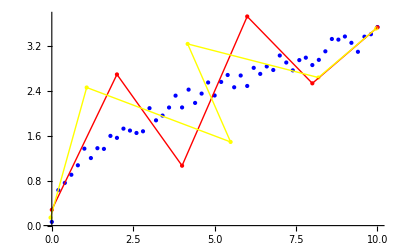

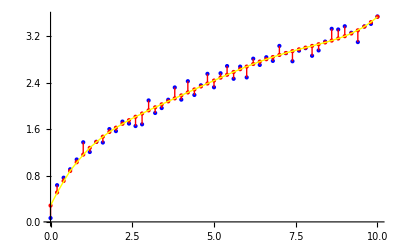

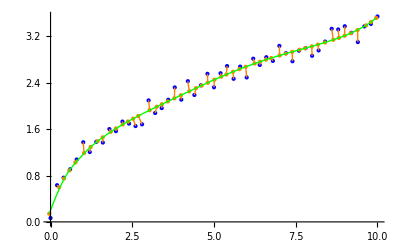

```mathematica
m = 50;
data2=Table[{t,Sqrt[t]+0.4RandomReal[]},{t,0.0,10.0,10/m}];
n=5;
uniformPoints  = findUParameters[data2];
uApproximationPoints = findLinearSol[data2,uniformPoints,n];

chordParameters = findCParameters[data2];
chordApproximationPoints = findLinearSol[data2,chordParameters,n];

dataPlot=ListPlot[data2,PlotStyle->{PointSize[Medium],Blue}];

uniPlot = ListPlot[uApproximationPoints,PlotStyle->{PointSize[Large],Red}];

chordPlot = ListPlot[chordApproximationPoints,PlotStyle->{PointSize[Large],Yellow}];

uniformPlot = ListLinePlot[uApproximationPoints,PlotStyle->{Red,Thick},PlotRange->All];

chordPlot1 = ListLinePlot[chordApproximationPoints,PlotStyle->{Yellow,Thick},PlotRange->All];

Show[{dataPlot,uniPlot,chordPlot,uniformPlot,chordPlot1},PlotRange->All]

uParametersOnCurve = Table[1*(1-uniformPoints[[i]])^5*uApproximationPoints[[1]]+
5*uniformPoints[[i]]^1*(1-uniformPoints[[i]])^4*uApproximationPoints[[2]]+
10*uniformPoints[[i]]^2*(1-uniformPoints[[i]])^3*uApproximationPoints[[3]]+
10*uniformPoints[[i]]^3*(1-uniformPoints[[i]])^2*uApproximationPoints[[4]]+
5*uniformPoints[[i]]^4*(1-uniformPoints[[i]])^1*uApproximationPoints[[5]]+
1*uniformPoints[[i]]^5*uApproximationPoints[[6]],
{i,1,Length[data2]}
];

dataPlot1=ListPlot[data2,PlotStyle->{PointSize[Medium],Blue}];
lineparameters = Graphics[{PointSize[Medium],Red,Point[uParametersOnCurve]}];
pplot = Table[Graphics[{PointSize[Medium],Red,Line[{uParametersOnCurve[[i]],data2[[i]]}]}],{i,1,Length[data2]}];
UPlot=Graphics[{Yellow,Thick,BezierCurve[uParametersOnCurve,SplineDegree-> n]}];
Show[dataPlot1,lineparameters, pplot,UPlot]

cParametersOnCurve = Table[1*(1-chordParameters[[i]])^5*chordApproximationPoints[[1]]+
5*chordParameters[[i]]^1*(1-chordParameters[[i]])^4*chordApproximationPoints[[2]]+
10*chordParameters[[i]]^2*(1-chordParameters[[i]])^3*chordApproximationPoints[[3]]+
10*chordParameters[[i]]^3*(1-chordParameters[[i]])^2*chordApproximationPoints[[4]]+
5*chordParameters[[i]]^4*(1-chordParameters[[i]])^1*chordApproximationPoints[[5]]+
1*chordParameters[[i]]^5*chordApproximationPoints[[6]],
{i,1,Length[data2]}
];

lineparameter= Graphics[{PointSize[Medium],Orange,Point[cParametersOnCurve]}];
prsplot = Table[Graphics[{PointSize[Medium],Orange,Line[{cParametersOnCurve[[i]],data2[[i]]}]}],{i,1,Length[data2]}];
chordparamPlot=Graphics[{Green,Thick,BezierCurve[cParametersOnCurve,SplineDegree-> n]}];
Show[dataPlot1,lineparameter, prsplot,chordparamPlot]
```

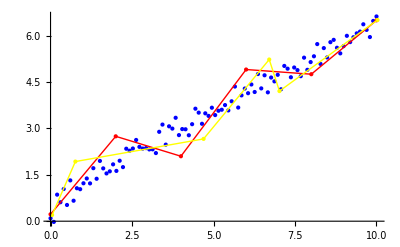

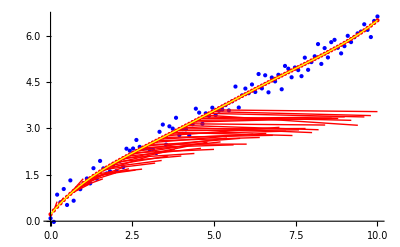

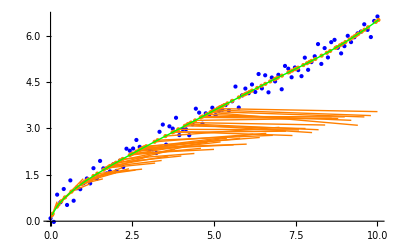

```mathematica
m = 99;
data3 = Table[{t,Sqrt[t]+0.4t - 0.3 Sqrt[t] + 0.6 RandomReal[] - 0.5RandomReal[]},{t,0.0,10.0,10/m}];
n=5;
uniformPoints  = findUParameters[data3];
uApproximationPoints = findLinearSol[data3,uniformPoints,n];

chordParameters = findCParameters[data3];
chordApproximationPoints = findLinearSol[data3,chordParameters,n];

dataPlot=ListPlot[data3,PlotStyle->{PointSize[Medium],Blue}];

uniPlot = ListPlot[uApproximationPoints,PlotStyle->{PointSize[Large],Red}];

chordPlot = ListPlot[chordApproximationPoints,PlotStyle->{PointSize[Large],Yellow}];

uniformPlot = ListLinePlot[uApproximationPoints,PlotStyle->{Red,Thick},PlotRange->All];

chordPlot1 = ListLinePlot[chordApproximationPoints,PlotStyle->{Yellow,Thick},PlotRange->All];

Show[{dataPlot,uniPlot,chordPlot,uniformPlot,chordPlot1},PlotRange->All]

uParametersOnCurve = Table[1*(1-uniformPoints[[i]])^5*uApproximationPoints[[1]]+
5*uniformPoints[[i]]^1*(1-uniformPoints[[i]])^4*uApproximationPoints[[2]]+
10*uniformPoints[[i]]^2*(1-uniformPoints[[i]])^3*uApproximationPoints[[3]]+
10*uniformPoints[[i]]^3*(1-uniformPoints[[i]])^2*uApproximationPoints[[4]]+
5*uniformPoints[[i]]^4*(1-uniformPoints[[i]])^1*uApproximationPoints[[5]]+
1*uniformPoints[[i]]^5*uApproximationPoints[[6]],
{i,1,Length[data3]}
];

dataPlot1=ListPlot[data3,PlotStyle->{PointSize[Medium],Blue}];
lineparameters = Graphics[{PointSize[Medium],Red,Point[uParametersOnCurve]}];
pplot = Table[Graphics[{PointSize[Medium],Red,Line[{uParametersOnCurve[[i]],data2[[i]]}]}],{i,1,Length[data2]}];
UPlot=Graphics[{Yellow,Thick,BezierCurve[uParametersOnCurve,SplineDegree-> n]}];
Show[dataPlot1,lineparameters, pplot,UPlot]

cParametersOnCurve = Table[1*(1-chordParameters[[i]])^5*chordApproximationPoints[[1]]+
5*chordParameters[[i]]^1*(1-chordParameters[[i]])^4*chordApproximationPoints[[2]]+
10*chordParameters[[i]]^2*(1-chordParameters[[i]])^3*chordApproximationPoints[[3]]+
10*chordParameters[[i]]^3*(1-chordParameters[[i]])^2*chordApproximationPoints[[4]]+
5*chordParameters[[i]]^4*(1-chordParameters[[i]])^1*chordApproximationPoints[[5]]+
1*chordParameters[[i]]^5*chordApproximationPoints[[6]],
{i,1,Length[data3]}
];

lineparameter= Graphics[{PointSize[Medium],Orange,Point[cParametersOnCurve]}];
prsplot = Table[Graphics[{PointSize[Medium],Orange,Line[{cParametersOnCurve[[i]],data2[[i]]}]}],{i,1,Length[data2]}];
chordparamPlot=Graphics[{Green,Thick,BezierCurve[cParametersOnCurve,SplineDegree-> n]}];
Show[dataPlot1,lineparameter, prsplot,chordparamPlot]
```

# Part : 3

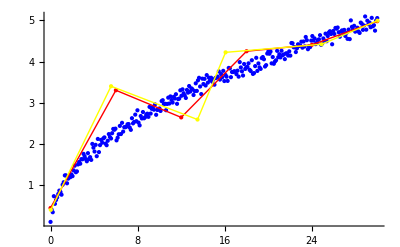

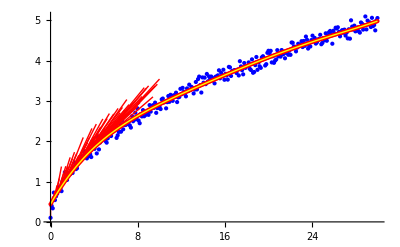

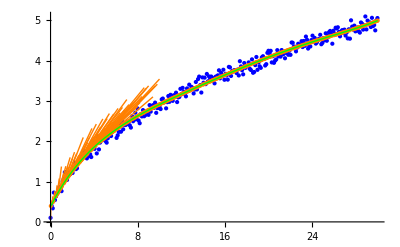

Part::partd: Part specification data5⟦50⟧ is longer than depth of object.

ListPlot::lpn: -1. data5⟦50⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification data5⟦50⟧ is longer than depth of object.

ListPlot::lpn: -1. data5⟦50⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification data5⟦50⟧ is longer than depth of object.

ListPlot::lpn: -0.0992958 data5⟦50⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification data5⟦50⟧ is longer than depth of object.

ListPlot::lpn: -0.0992958 data5⟦50⟧ is not a list of numbers or pairs of numbers.

```mathematica
m = 99;
data5 = Table[{t,0.3Sqrt[t]+0.6 Sqrt[t]-0.2 RandomReal[]+0.3 RandomReal[]},{t,0.0,30.0,10/m}];
n=5;
uniformPoints  = findUParameters[data5];
uApproximationPoints = findLinearSol[data5,uniformPoints,n];

chordParameters = findCParameters[data5];
chordApproximationPoints = findLinearSol[data5,chordParameters,n];

dataPlot=ListPlot[data5,PlotStyle->{PointSize[Medium],Blue}];

uniPlot = ListPlot[uApproximationPoints,PlotStyle->{PointSize[Large],Red}];

chordPlot = ListPlot[chordApproximationPoints,PlotStyle->{PointSize[Large],Yellow}];

uniformPlot = ListLinePlot[uApproximationPoints,PlotStyle->{Red,Thick},PlotRange->All];

chordPlot1 = ListLinePlot[chordApproximationPoints,PlotStyle->{Yellow,Thick},PlotRange->All];

Show[{dataPlot,uniPlot,chordPlot,uniformPlot,chordPlot1},PlotRange->All]

uParametersOnCurve = Table[1*(1-uniformPoints[[i]])^5*uApproximationPoints[[1]]+
5*uniformPoints[[i]]^1*(1-uniformPoints[[i]])^4*uApproximationPoints[[2]]+
10*uniformPoints[[i]]^2*(1-uniformPoints[[i]])^3*uApproximationPoints[[3]]+
10*uniformPoints[[i]]^3*(1-uniformPoints[[i]])^2*uApproximationPoints[[4]]+
5*uniformPoints[[i]]^4*(1-uniformPoints[[i]])^1*uApproximationPoints[[5]]+
1*uniformPoints[[i]]^5*uApproximationPoints[[6]],
{i,1,Length[data5]}
];

dataPlot1=ListPlot[data5,PlotStyle->{PointSize[Medium],Blue}];
lineparameters = Graphics[{PointSize[Medium],Red,Point[uParametersOnCurve]}];
pplot = Table[Graphics[{PointSize[Medium],Red,Line[{uParametersOnCurve[[i]],data2[[i]]}]}],{i,1,Length[data2]}];
UPlot=Graphics[{Yellow,Thick,BezierCurve[uParametersOnCurve,SplineDegree-> n]}];
Show[dataPlot1,lineparameters, pplot,UPlot]

cParametersOnCurve = Table[1*(1-chordParameters[[i]])^5*chordApproximationPoints[[1]]+
5*chordParameters[[i]]^1*(1-chordParameters[[i]])^4*chordApproximationPoints[[2]]+
10*chordParameters[[i]]^2*(1-chordParameters[[i]])^3*chordApproximationPoints[[3]]+
10*chordParameters[[i]]^3*(1-chordParameters[[i]])^2*chordApproximationPoints[[4]]+
5*chordParameters[[i]]^4*(1-chordParameters[[i]])^1*chordApproximationPoints[[5]]+
1*chordParameters[[i]]^5*chordApproximationPoints[[6]],
{i,1,Length[data5]}
];

lineparameter= Graphics[{PointSize[Medium],Orange,Point[cParametersOnCurve]}];
prsplot = Table[Graphics[{PointSize[Medium],Orange,Line[{cParametersOnCurve[[i]],data2[[i]]}]}],{i,1,Length[data2]}];
chordparamPlot=Graphics[{Green,Thick,BezierCurve[cParametersOnCurve,SplineDegree-> n]}];
Manipulate[ ListPlot[a data5[[50]],PlotStyle->{PointSize[Medium],Blue}],{a,-1,1}]
Show[dataPlot1,lineparameter, prsplot,chordparamPlot]
```

# Part: 4

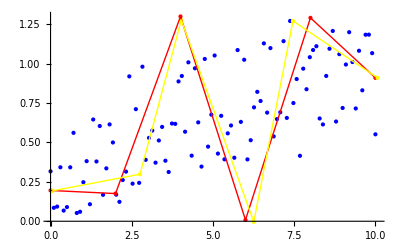

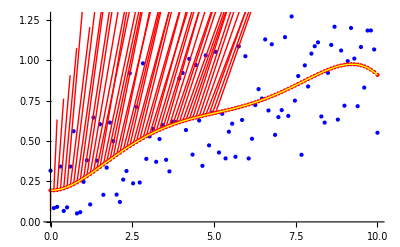

```mathematica
m = 99;
data6 = Table[{t,0.2Sqrt[t]+0.4Sqrt[t] - 0.3 Sqrt[t] + 0.6 RandomReal[] - 0.5RandomReal[]},{t,0.0,10.0,10/m}];
n=5;
uniformPoints  = findUParameters[data6];
uApproximationPoints = findLinearSol[data6,uniformPoints,n];

chordParameters = findCParameters[data6];
chordApproximationPoints = findLinearSol[data6,chordParameters,n];

dataPlot=ListPlot[data6,PlotStyle->{PointSize[Medium],Blue}];

uniPlot = ListPlot[uApproximationPoints,PlotStyle->{PointSize[Large],Red}];

chordPlot = ListPlot[chordApproximationPoints,PlotStyle->{PointSize[Large],Yellow}];

uniformPlot = ListLinePlot[uApproximationPoints,PlotStyle->{Red,Thick},PlotRange->All];

chordPlot1 = ListLinePlot[chordApproximationPoints,PlotStyle->{Yellow,Thick},PlotRange->All];

Show[{dataPlot,uniPlot,chordPlot,uniformPlot,chordPlot1},PlotRange->All]

uParametersOnCurve = Table[1*(1-uniformPoints[[i]])^5*uApproximationPoints[[1]]+
5*uniformPoints[[i]]^1*(1-uniformPoints[[i]])^4*uApproximationPoints[[2]]+
10*uniformPoints[[i]]^2*(1-uniformPoints[[i]])^3*uApproximationPoints[[3]]+
10*uniformPoints[[i]]^3*(1-uniformPoints[[i]])^2*uApproximationPoints[[4]]+
5*uniformPoints[[i]]^4*(1-uniformPoints[[i]])^1*uApproximationPoints[[5]]+
1*uniformPoints[[i]]^5*uApproximationPoints[[6]],
{i,1,Length[data6]}
];

dataPlot1=ListPlot[data6,PlotStyle->{PointSize[Medium],Blue}];
lineparameters = Graphics[{PointSize[Medium],Red,Point[uParametersOnCurve]}];
pplot = Table[Graphics[{PointSize[Medium],Red,Line[{uParametersOnCurve[[i]],data2[[i]]}]}],{i,1,Length[data2]}];
UPlot=Graphics[{Yellow,Thick,BezierCurve[uParametersOnCurve,SplineDegree-> n]}];
Show[dataPlot1,lineparameters, pplot,UPlot]

cParametersOnCurve = Table[1*(1-chordParameters[[i]])^5*chordApproximationPoints[[1]]+
5*chordParameters[[i]]^1*(1-chordParameters[[i]])^4*chordApproximationPoints[[2]]+
10*chordParameters[[i]]^2*(1-chordParameters[[i]])^3*chordApproximationPoints[[3]]+
10*chordParameters[[i]]^3*(1-chordParameters[[i]])^2*chordApproximationPoints[[4]]+
5*chordParameters[[i]]^4*(1-chordParameters[[i]])^1*chordApproximationPoints[[5]]+
1*chordParameters[[i]]^5*chordApproximationPoints[[6]],
{i,1,Length[data6]}
];

lineparameter= Graphics[{PointSize[Medium],Orange,Point[cParametersOnCurve]}];
prsplot = Table[Graphics[{PointSize[Medium],Orange,Line[{cParametersOnCurve[[i]],data2[[i]]}]}],{i,1,Length[data2]}];
chordparamPlot=Graphics[{Green,Thick,BezierCurve[cParametersOnCurve,SplineDegree-> n]}];
Manipulate[ ListPlot[a data6[[50] + b],PlotStyle->{PointSize[Medium],Blue}],{a,1,10}, {b,1,10}];
Show[dataPlot1,lineparameter, prsplot,chordparamPlot]
```